```mathematica
A=2.0; phi=0
```

0

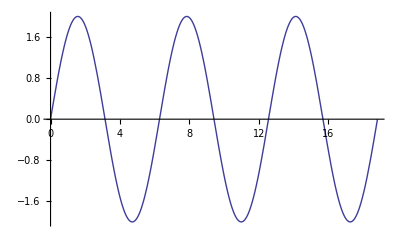

```mathematica
Plot[A*Sin[t+phi],{t,0,6Pi}]
```

```mathematica
small Omega
```

Omega small

```mathematica
freq= 1/(2*Pi)
```

1/(2 π)

```mathematica
N[%]
```

0.159155

```mathematica
ω = 2*Pi*freq
```

1

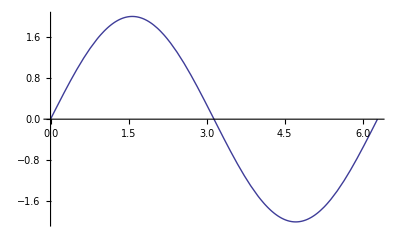

```mathematica
Wave =Plot[A*Sin[ω*t+phi],{t,0,2*Pi}]
```

```mathematica
(*Right Arrow = Esc  - > Esc*)
```

```mathematica
Animate[Plot[A*Sin[ω*t+phi],{t,0,2*Pi}],{ω,0,10},{phi,0,2 π},AnimationRunning ->False]
```

```mathematica
Velocity=2; λ= 3.0;
```

```mathematica
Freq= Velocity/λ
```

0.666667

```mathematica
Period =1/Freq
```

1.5

```mathematica
wave:= A*Sin[(2*Pi/λ)*(x-Velocity*t)]
```

```mathematica
Plot3D[ Sin[(2*Pi/λ)*(x-Velocity*t)],{x,0,6},{t,0,7}, AxesLabel->Automatic ]
```

-Graphics3D-

```mathematica
Plot3D[wave,{x,0,6},{t,0,7} ,AxesLabel->Automatic ]
```

-Graphics3D-

```mathematica
(* Let's select light with velocity = c and a wavelength of 400 nm  *)
```

```mathematica
Velocity = 2.998*10^8
```

2.998×10^8

```mathematica
(* Remember to work in meters *)
```

```mathematica
λ= 400*10^-9
```

1/2500000

```mathematica
Plot3D[ Sin[(2*Pi/λ)*(x-Velocity*t)],{x,0,2*λ},{t,0,2*λ/Velocity}]
```

-Graphics3D-

```mathematica
Freq=Velocity/λ
```

7.495×10^14

```mathematica
Period = 1/Freq
```

1.33422×10^-15

```mathematica
wave2==Sin[(2*Pi/λ)*(x-Velocity*t)]
```

wave2==Sin[5000000 π (-2.998×10^8 t+x)]

```mathematica
λminmn =100;
```

```mathematica
λmaxnm=1000;
```

```mathematica
f=Velocity/(λmaxnm*10^-9)
```

2.998×10^14

```mathematica
pmax=1/f
```

3.33556×10^-15

```mathematica
Animate[Plot3D[Sin[(2*Pi/λ)*(x-Velocity*t)],{x,0,λmaxnm*10^-9},{t,0,pmax},AxesLabel->Automatic  ],{λ,λminmn*10^-9, λmaxnm*10^-9},AnimationRunning ->False]
```